BISECTION METHOD

```mathematica
Ques1.Find the root of x^3+4x+1 = 0 approximately upto 25 iterations using Bisection  Method. Let X[0] = -2 and X[1] = 0. Also Plot the Graph.
```

1th iteration value is : -1

Estimated error in 1th iteration is : 1

2th iteration value is : -1/2

Estimated error in 2th iteration is : 1/2

3th iteration value is : -1/4

Estimated error in 3th iteration is : 1/4

4th iteration value is : -1/8

Estimated error in 4th iteration is : 1/8

5th iteration value is : -3/16

Estimated error in 5th iteration is : 1/16

6th iteration value is : -7/32

Estimated error in 6th iteration is : 1/32

7th iteration value is : -15/64

Estimated error in 7th iteration is : 1/64

8th iteration value is : -31/128

Estimated error in 8th iteration is : 1/128

9th iteration value is : -63/256

Estimated error in 9th iteration is : 1/256

10th iteration value is : -127/512

Estimated error in 10th iteration is : 1/512

Return[-253/1024]

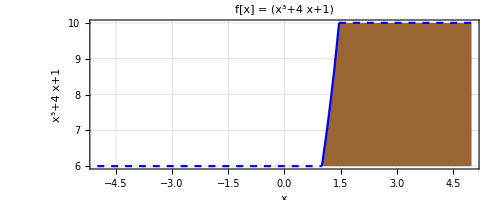

```mathematica
x0 = -2;
x1 = 0;
Nmax = 25;
eps = 0.001; 
f[x_] := x ^3 + 4x + 1; If[N[f[x0] * f[x1]] > 0, 
Print["These values do not satisfy the IVP so change the values."],
For [i = 1, i ≤ Nmax, i++, a = (x0 + x1) / 2; 
If[Abs[(x1 - x0) / 2] < eps, Return[a],
Print[i, "th iteration value is : ", a]; 
Print[" Estimated error in ", i, "th iteration is : ", (x1 - x0) / 2]; 
If[f[a] * f[x1] > 0, x1 = a, x0 = a]]];
Print[" Root is : ", a];
Print[" Estimated error in ", i, "th iteration is : ", (x1 - x0) / 2]] 
Plot[f[x], {x, -5, 5}, PlotRange -> {10, 6}, 
PlotStyle -> Blue, PlotLabel -> "f[x] = " f[x], AxesLabel -> {x, f[x]},
AspectRatio -> Automatic, Frame -> True, GridLines -> Automatic,
ClippingStyle -> Automatic, Filling -> Axis, FillingStyle -> Brown]
```